## Forcing the frequencies

```mathematica
eq1:=X[r]+2G[r]-2A[r]==Subscript[X, i]*r^i;
eq2:=X'[r]-2A'[r]-2G[r]A[r]+2G[r]X[r]-2 G[r]^2==X'[r]-2G'[r]+G[r]X[r]-G[r]A[r]-2 G[r]^2-A[r]^2+A[r]X[r];
eq3:=A[r]+X[r]-G[r]==Subscript[L, j]*r^j;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

2 A[r]+r^i X_i==2 G[r]+X[r]

(A[r]-G[r]) (A[r]-X[r])+2 G'[r]==2 A'[r]

A[r]+X[r]==G[r]+r^j L_j

```mathematica
Solve[eq1,X[r]]
```

{{X[r]→2 A[r]-2 G[r]+r^i X_i}}

```mathematica
X[r_]:=2 A[r]-2 G[r]+r^i Subscript[X, i];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

(A[r]-G[r]) (A[r]-2 G[r]+r^i X_i)+2 (A'[r]-G'[r])==0

3 A[r]+r^i X_i==3 G[r]+r^j L_j

```mathematica
Solve[eq3,A[r]]
```

{{A[r]→1/3 (3 G[r]+r^j L_j-r^i X_i)}}

```mathematica
A[r_]:=1/3 (3 G[r]+r^j Subscript[L, j]-r^i Subscript[X, i]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

r^(-1+j) L_j (6 j+r (-3 G[r]+r^j L_j+r^i X_i))==r^(-1+i) X_i (6 i-3 r G[r]+2 r^(1+i) X_i)

True

```mathematica
FullSimplify[Solve[eq2,G[r]]]
```

{{G[r]→1/3 ((6 i)/r+r^j L_j+2 r^i X_i+(6 (-i+j) L_j)/(r (L_j-r^(i-j) X_i)))}}

```mathematica
G[r_]:=1/3 ((6 i)/r+r^j Subscript[L, j]+2 r^i Subscript[X, i]+(6 (-i+j) Subscript[L, j])/(r (Subscript[L, j]-r^(i-j) Subscript[X, i])));
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
```

True

True

True

```mathematica
FullSimplify[A[r]]
FullSimplify[G[r]]
FullSimplify[X[r]]
```

1/3 ((6 i)/r+2 r^j L_j+r^i X_i+(6 (-i+j) L_j)/(r (L_j-r^(i-j) X_i)))

1/3 ((6 i)/r+r^j L_j+2 r^i X_i+(6 (-i+j) L_j)/(r (L_j-r^(i-j) X_i)))

1/3 (2 r^j L_j+r^i X_i)

```mathematica
HC1:=B''[r]+B[r]*(X'[r]-2*A'[r])+B'[r]*(-2*A[r]+X[r]+2*G[r])-2*G[r]*B[r]*(A[r]-X[r]+G[r]);
HC2:=F''[r]+F[r]*(X'[r]-2*G'[r])+F'[r]*(A[r]+X[r]-G[r])+F[r]*(G[r]*(X[r]-A[r]-2G[r])-A[r]*(A[r]-X[r]))-G[r];
FullSimplify[HC1==0]
FullSimplify[HC2==0]
```

r^i X_i B'[r]+B''[r]==1/9 B[r] ((36 i (-1+4 i))/r^2+2 r^(-1+j) L_j (54 i-33 j+r^(1+j) L_j)+r^(-1+i) (75 i+8 r^(1+j) L_j) X_i+8 r^(2 i) X_i^2+(108 (i-j)^2 r^(-2+2 j) L_j^2)/((r^j L_j-r^i X_i)^2)-(36 (i-j) L_j (-1+7 i+j+3 r^(1+j) L_j))/(r^2 (L_j-r^(i-j) X_i)))

2 r^(1+3 j) F[r] L_j^3+3 r^(2 j) L_j^2 (r+2 F[r] (7 j+r^(1+i) X_i)-3 r F'[r])+3 r^(-1+j) L_j (6 j (r+(-2+8 j) F[r])+(36 (i-j)^2 r^i F[r] X_i)/(r^j L_j-r^i X_i)+r^(1+i) X_i (r-11 (i-2 j) F[r]+3 r F'[r])-3 r^2 F''[r])+r^(-1+i) X_i (-18 i (r+(-2+8 i) F[r])-3 r^(1+i) (2 r+25 i F[r]) X_i-8 r^(2+2 i) F[r] X_i^2+9 r^2 F''[r])==0

It is possible to solve the first equation for the special case i = j, however the second equation can not be solved without specifying the values of i = j

```mathematica
i=j;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
```

B[r] ((36 j (-1+4 j))/r+r^j (42 j L_j+75 j X_j+2 r^(1+j) (L_j+2 X_j)^2))==9 r (r^j X_j B'[r]+B''[r])

{{B[r]→2^((9 j)/(2 (1+j))) ⅇ^(-1/6 r^(1+j) ((3 X_j)/(1+j)+(√(8 L_j^2+32 L_j X_j+41 X_j^2))/(√((1+j)^2)))) r^(-j/2) (r^(1+j))^((9 j)/(2 (1+j))) (C[1] HypergeometricU[1/2 j (9/(1+j)+(28 L_j+53 X_j)/(√((1+j)^2) √(8 L_j^2+32 L_j X_j+41 X_j^2))),(9 j)/(1+j),(r^(1+j) √(8 L_j^2+32 L_j X_j+41 X_j^2))/(3 √((1+j)^2))]+C[2] LaguerreL[1/2 j (-9/(1+j)+(-28 L_j-53 X_j)/(√((1+j)^2) √(8 L_j^2+32 L_j X_j+41 X_j^2))),8-9/(1+j),(r^(1+j) √(8 L_j^2+32 L_j X_j+41 X_j^2))/(3 √((1+j)^2))])}}

```mathematica
FullSimplify[HC2==0]
```

18 j+(36 j (-1+4 j) F[r])/r+2 r^(1+2 j) F[r] (L_j+2 X_j)^2+3 r^j ((2 r+25 j F[r]) X_j+L_j (r+14 j F[r]-3 r F'[r]))==9 r F''[r]

### Checking i = j = 0

```mathematica
i=0;
j=0;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

2 B[r] (L_0+2 X_0)^2==9 (X_0 B'[r]+B''[r])

{{B[r]→ⅇ^(-1/6 r (3 X_0+√(8 L_0^2+32 L_0 X_0+41 X_0^2))) (C[1]+ⅇ^(1/3 r √(8 L_0^2+32 L_0 X_0+41 X_0^2)) C[2])}}

(L_0+2 X_0) (3+2 F[r] (L_0+2 X_0))==9 (L_0 F'[r]+F''[r])

{{F[r]→ⅇ^(-1/6 r (3 L_0+√(17 L_0^2+32 L_0 X_0+32 X_0^2))) (C[1]+ⅇ^(1/3 r √(17 L_0^2+32 L_0 X_0+32 X_0^2)) C[2])-3/(2 L_0+4 X_0)}}

### Case i = j = -1

```mathematica
i=-1;
j=-1;
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

9 (X_-1 B'[r]+r B''[r])==(B[r] (2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))/r

{{B[r]→r^(1/6 (3-3 X_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[1]+r^(1/6 (3-3 X_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[2]}}

18+L_-1 (-3+9 F'[r])+9 r F''[r]==6 X_-1+(F[r] (2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))/r

{{F[r]→r^(1/6 (3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[1]+r^(1/6 (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[2]-(3 r (-6+L_-1+2 X_-1))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1))}}

```mathematica
B[r_]:=r^(1/6 (3-3 Subscript[X, -1]-√(-2 (-15+Subscript[L, -1]) (-6+Subscript[L, -1])+(75-8 Subscript[L, -1]) Subscript[X, -1]-8 Subscript[X, -1]^2) √((-729-8 Subscript[L, -1]^2+8 Subscript[L, -1] (21-4 Subscript[X, -1])+(318-41 Subscript[X, -1]) Subscript[X, -1])/(2 (-15+Subscript[L, -1]) (-6+Subscript[L, -1])+(-75+8 Subscript[L, -1]) Subscript[X, -1]+8 Subscript[X, -1]^2)))) C[1]+r^(1/6 (3-3 Subscript[X, -1]+√(-2 (-15+Subscript[L, -1]) (-6+Subscript[L, -1])+(75-8 Subscript[L, -1]) Subscript[X, -1]-8 Subscript[X, -1]^2) √((-729-8 Subscript[L, -1]^2+8 Subscript[L, -1] (21-4 Subscript[X, -1])+(318-41 Subscript[X, -1]) Subscript[X, -1])/(2 (-15+Subscript[L, -1]) (-6+Subscript[L, -1])+(-75+8 Subscript[L, -1]) Subscript[X, -1]+8 Subscript[X, -1]^2)))) C[2];
F[r_]:=r^(1/6 (3-3 Subscript[L, -1]-√(-2 (-15+Subscript[L, -1]) (-6+Subscript[L, -1])+(75-8 Subscript[L, -1]) Subscript[X, -1]-8 Subscript[X, -1]^2) √(-4-(9 (-1+Subscript[L, -1])^2)/(2 (-15+Subscript[L, -1]) (-6+Subscript[L, -1])+(-75+8 Subscript[L, -1]) Subscript[X, -1]+8 Subscript[X, -1]^2)))) C[3]+r^(1/6 (3-3 Subscript[L, -1]+√(-2 (-15+Subscript[L, -1]) (-6+Subscript[L, -1])+(75-8 Subscript[L, -1]) Subscript[X, -1]-8 Subscript[X, -1]^2) √(-4-(9 (-1+Subscript[L, -1])^2)/(2 (-15+Subscript[L, -1]) (-6+Subscript[L, -1])+(-75+8 Subscript[L, -1]) Subscript[X, -1]+8 Subscript[X, -1]^2)))) C[4]-(3 r (-6+Subscript[L, -1]+2 Subscript[X, -1]))/(180+2 Subscript[L, -1]^2+Subscript[X, -1] (-75+8 Subscript[X, -1])+Subscript[L, -1] (-51+8 Subscript[X, -1]));
```

```mathematica
Rtt[r_]:=B'[r]+B[r]*(2*G[r]+X[r]-A[r]);
Rrr[r_]:=A'[r]+2G'[r]+A[r]A[r]+2G[r]G[r]-A[r]X[r]-2X[r]G[r];
Rthth[r_]:=F'[r]+F[r](A[r]+X[r])+1;
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 r^(1/6 (-3-3 X_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) (C[1] (-9+4 L_-1+5 X_-1)+r^(1/3 √(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))) C[2] (-9+4 L_-1+5 X_-1)-C[1] √(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))+r^(1/3 √(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))) C[2] √(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))

(162-2 L_-1^2-2 L_-1 (12+X_-1)+X_-1 (-57+4 X_-1))/(9 r^2)

1-(3 (-6+L_-1+2 X_-1))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1))+1/(3 r)2 (-3+2 L_-1+X_-1) (r^(1/6 (3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[3]+r^(1/6 (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[4]-(3 r (-6+L_-1+2 X_-1))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1)))+1/6 r^(1/6 (-3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[4] (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))-1/6 r^(1/6 (-3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[3] (-3+3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))

## Auto-parallel curves

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*θ'[τ]^2+F[r[τ]]*ϕ'[τ]^2*Sin[θ]^2;
FullSimplify[eq1r[τ]]
eq1th[τ_]=θ''[τ]+2*G[r[τ]]*θ'[τ]*r'[τ]-Cos[θ]*Sin[θ]*ϕ'[τ]^2;
FullSimplify[eq1th[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ]+Cos[θ]/Sin[θ]*ϕ'[τ]*θ'[τ];
FullSimplify[eq1ph[τ]]
```

(2 (-6+2 L_-1+X_-1) r'[τ] t'[τ])/(3 r[τ])+t''[τ]

((2 L_-1+X_-1) r'[τ]^2)/(3 r[τ])+C[1] r[τ]^(1/6 (3-3 X_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) t'[τ]^2+C[2] r[τ]^(1/6 (3-3 X_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) t'[τ]^2+C[3] r[τ]^(1/6 (3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2)+C[4] r[τ]^(1/6 (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2)-(3 r[τ] (-6+L_-1+2 X_-1) (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1))+r''[τ]

(2 (-6+L_-1+2 X_-1) r'[τ] θ'[τ])/(3 r[τ])-Cos[θ] Sin[θ] ϕ'[τ]^2+θ''[τ]

(2 (-6+L_-1+2 X_-1) r'[τ] ϕ'[τ])/(3 r[τ])+Cot[θ] θ'[τ] ϕ'[τ]+ϕ''[τ]

Fixing θ=π/2

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

(2 (-6+2 L_-1+X_-1) r'[τ] t'[τ])/(3 r[τ])+t''[τ]

((2 L_-1+X_-1) r'[τ]^2)/(3 r[τ])+(C[1] r[τ]^(1/6 (3-3 X_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))+C[2] r[τ]^(1/6 (3-3 X_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))) t'[τ]^2+(C[3] r[τ]^(1/6 (3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))+C[4] r[τ]^(1/6 (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))-(3 r[τ] (-6+L_-1+2 X_-1))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1))) ϕ'[τ]^2+r''[τ]

(2 (-6+L_-1+2 X_-1) r'[τ] ϕ'[τ])/(3 r[τ])+ϕ''[τ]

```mathematica
DSolve[(2 (-6+Subscript[L, -1]+2 Subscript[X, -1]) r'[τ] ϕ'[τ])/(3 r[τ])+ϕ''[τ]==0,ϕ[τ],τ]
```

{{ϕ[τ]→C[2]+C[1] r[K[1]]^(-2/3 (-6+L_-1+2 X_-1))K[1]1τ}}

```mathematica
D[C[4]+C[3] r[K[1]]^(-2/3 (-6+Subscript[L, -1]+2 Subscript[X, -1]))K[1]1τ,τ]
```

C[3] r[τ]^(-2/3 (-6+L_-1+2 X_-1))

```mathematica
ϕ[τ_]:=C[6]+C[5] r[K[1]]^(-2/3 (-6+Subscript[L, -1]+2 Subscript[X, -1]))K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

(2 (-6+2 L_-1+X_-1) r'[τ] t'[τ])/(3 r[τ])+t''[τ]

C[5]^2 r[τ]^(-4/3 (-6+L_-1+2 X_-1)) (C[3] r[τ]^(1/6 (3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))+C[4] r[τ]^(1/6 (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))-(3 r[τ] (-6+L_-1+2 X_-1))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1)))+((2 L_-1+X_-1) r'[τ]^2)/(3 r[τ])+(C[1] r[τ]^(1/6 (3-3 X_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))+C[2] r[τ]^(1/6 (3-3 X_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))) t'[τ]^2+r''[τ]

0

```mathematica
DSolve[(2 (-6+2 Subscript[L, -1]+Subscript[X, -1]) r'[τ] t'[τ])/(3 r[τ])+t''[τ]==0,t[τ],τ]
```

{{t[τ]→C[2]+C[1] r[K[1]]^(-2/3 (-6+2 L_-1+X_-1))K[1]1τ}}

```mathematica
D[C[8]+C[7] r[K[1]]^(-2/3 (-6+2 Subscript[L, -1]+Subscript[X, -1]))K[1]1τ,τ]
```

C[7] r[τ]^(-2/3 (-6+2 L_-1+X_-1))

```mathematica
t[τ_]:=C[8]+C[7] r[K[1]]^(-2/3 (-6+2 Subscript[L, -1]+Subscript[X, -1]))K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

0

C[7]^2 r[τ]^(-4/3 (-6+2 L_-1+X_-1)) (C[1] r[τ]^(1/6 (3-3 X_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))+C[2] r[τ]^(1/6 (3-3 X_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))))+C[5]^2 r[τ]^(-4/3 (-6+L_-1+2 X_-1)) (C[3] r[τ]^(1/6 (3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))+C[4] r[τ]^(1/6 (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))))-(3 r[τ] (-6+L_-1+2 X_-1))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1)))+((2 L_-1+X_-1) r'[τ]^2)/(3 r[τ])+r''[τ]

0

A numerical computation

21/260 r[τ]^(31/3)+r[τ]^(44/3-(√233)/3)+r[τ]^(1/3 (44+√233))+r[τ]^(34/3-(√269)/3)+r[τ]^(1/3 (34+√269))-(5 r'[τ]^2)/(3 r[τ])+r''[τ]

{{r[τ]→InterpolatingFunction[…][τ]}}

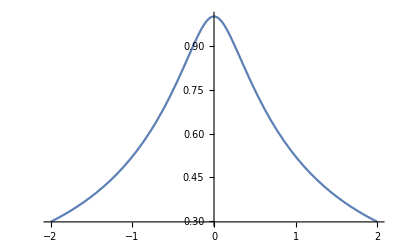

```mathematica
Subscript[X, -1]=1;Subscript[L, -1]=-3;
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]/.{C[1]->1,C[2]->1,C[3]->1,C[4]->1,C[5]->1,C[6]->1,C[7]->1,C[8]->1}]
s=NDSolve[{%==0,r[0]==1,r'[0]==0},r[τ],{τ,-2,2}]
Plot[r[τ]/.s,{τ,-2,2}]
```

```mathematica
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 r^(1/6 (-3-3 X_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) (C[1] (-9+4 L_-1+5 X_-1)+r^(1/3 √(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))) C[2] (-9+4 L_-1+5 X_-1)-C[1] √(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))+r^(1/3 √(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2))) C[2] √(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √((-729-8 L_-1^2+8 L_-1 (21-4 X_-1)+(318-41 X_-1) X_-1)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))

(162-2 L_-1^2-2 L_-1 (12+X_-1)+X_-1 (-57+4 X_-1))/(9 r^2)

1-(3 (-6+L_-1+2 X_-1))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1))+1/(3 r)2 (-3+2 L_-1+X_-1) (r^(1/6 (3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[3]+r^(1/6 (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[4]-(3 r (-6+L_-1+2 X_-1))/(180+2 L_-1^2+X_-1 (-75+8 X_-1)+L_-1 (-51+8 X_-1)))+1/6 r^(1/6 (-3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[4] (3-3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))-1/6 r^(1/6 (-3-3 L_-1-√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))) C[3] (-3+3 L_-1+√(-2 (-15+L_-1) (-6+L_-1)+(75-8 L_-1) X_-1-8 X_-1^2) √(-4-(9 (-1+L_-1)^2)/(2 (-15+L_-1) (-6+L_-1)+(-75+8 L_-1) X_-1+8 X_-1^2)))

In the limit for the above special case leads to

```mathematica
Limit[Rtt[r],r->∞]
FullSimplify[Limit[Rrr[r],r->∞]]
Limit[Rthth[r],r->∞]
```

$Aborted

0

$Aborted

De Sitter metric

```mathematica
gtt[r_]:=-(1-(2*a)/r-b*r^2);
grr[r_]:=1/(1-(2*a)/r-b*r^2) ;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b ∞

0

∞

Anti de Sitter

```mathematica
gtt[r_]:=-(1-a/r+b*r^2);
grr[r_]:=1/(1-a/r+b*r^2) ;
gthth[r_]:=r^2;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b (-∞)

0

∞